```mathematica
(*利用四阶泰勒级数方法求解常微分方程，x'=1+x^2-t^3,x(0)=-1*)
```

{{0.01,-0.980197},{0.02,-0.960779},{0.03,-0.941731},{0.04,-0.923038},{0.05,-0.904688},{0.06,-0.886667},{0.07,-0.868965},{0.08,-0.851568},{0.09,-0.834468},{0.1,-0.817653},{0.11,-0.801114},{0.12,-0.784841},{0.13,-0.768826},{0.14,-0.75306},{0.15,-0.737536},{0.16,-0.722246},{0.17,-0.707183},{0.18,-0.69234},{0.19,-0.677711},{0.2,-0.663289},{0.21,-0.64907},{0.22,-0.635047},{0.23,-0.621216},{0.24,-0.607571},{0.25,-0.594108},{0.26,-0.580823},{0.27,-0.567711},{0.28,-0.554769},{0.29,-0.541993},{0.3,-0.529381},{0.31,-0.516928},{0.32,-0.504631},{0.33,-0.492489},{0.34,-0.480498},{0.35,-0.468657},{0.36,-0.456962},{0.37,-0.445413},{0.38,-0.434007},{0.39,-0.422743},{0.4,-0.411619},{0.41,-0.400634},{0.42,-0.389787},{0.43,-0.379076},{0.44,-0.368502},{0.45,-0.358064},{0.46,-0.347761},{0.47,-0.337592},{0.48,-0.327558},{0.49,-0.317658},{0.5,-0.307893},{0.51,-0.298262},{0.52,-0.288767},{0.53,-0.279407},{0.54,-0.270183},{0.55,-0.261096},{0.56,-0.252147},{0.57,-0.243337},{0.58,-0.234667},{0.59,-0.226139},{0.6,-0.217753},{0.61,-0.209511},{0.62,-0.201415},{0.63,-0.193467},{0.64,-0.185668},{0.65,-0.178021},{0.66,-0.170527},{0.67,-0.16319},{0.68,-0.156011},{0.69,-0.148993},{0.7,-0.142138},{0.71,-0.135449},{0.72,-0.12893},{0.73,-0.122583},{0.74,-0.116411},{0.75,-0.110418},{0.76,-0.104606},{0.77,-0.0989794},{0.78,-0.0935417},{0.79,-0.0882967},{0.8,-0.0832479},{0.81,-0.0783994},{0.82,-0.0737551},{0.83,-0.0693193},{0.84,-0.0650962},{0.85,-0.0610901},{0.86,-0.0573056},{0.87,-0.0537471},{0.88,-0.0504194},{0.89,-0.0473273},{0.9,-0.0444757},{0.91,-0.0418695},{0.92,-0.0395137},{0.93,-0.0374137},{0.94,-0.0355747},{0.95,-0.0340019},{0.96,-0.0327009},{0.97,-0.0316771},{0.98,-0.0309361},{0.99,-0.0304837},{1.,-0.0303254},{1.01,-0.0304672},{1.02,-0.0309149},{1.03,-0.0316742},{1.04,-0.0327513},{1.05,-0.0341521},{1.06,-0.0358825},{1.07,-0.0379486},{1.08,-0.0403566},{1.09,-0.0431123},{1.1,-0.046222},{1.11,-0.0496916},{1.12,-0.0535272},{1.13,-0.0577349},{1.14,-0.0623205},{1.15,-0.0672901},{1.16,-0.0726494},{1.17,-0.0784043},{1.18,-0.0845606},{1.19,-0.0911238},{1.2,-0.0980995},{1.21,-0.105493},{1.22,-0.11331},{1.23,-0.121555},{1.24,-0.130233},{1.25,-0.13935},{1.26,-0.148909},{1.27,-0.158915},{1.28,-0.169373},{1.29,-0.180286},{1.3,-0.191658},{1.31,-0.203492},{1.32,-0.215793},{1.33,-0.228561},{1.34,-0.241801},{1.35,-0.255515},{1.36,-0.269704},{1.37,-0.28437},{1.38,-0.299514},{1.39,-0.315137},{1.4,-0.33124},{1.41,-0.347823},{1.42,-0.364885},{1.43,-0.382425},{1.44,-0.400443},{1.45,-0.418937},{1.46,-0.437905},{1.47,-0.457344},{1.48,-0.477251},{1.49,-0.497623},{1.5,-0.518456},{1.51,-0.539746},{1.52,-0.561487},{1.53,-0.583675},{1.54,-0.606303},{1.55,-0.629366},{1.56,-0.652856},{1.57,-0.676767},{1.58,-0.701091},{1.59,-0.72582},{1.6,-0.750945},{1.61,-0.776459},{1.62,-0.80235},{1.63,-0.828611},{1.64,-0.85523},{1.65,-0.882198},{1.66,-0.909503},{1.67,-0.937136},{1.68,-0.965084},{1.69,-0.993337},{1.7,-1.02188},{1.71,-1.05071},{1.72,-1.0798},{1.73,-1.10915},{1.74,-1.13875},{1.75,-1.16857},{1.76,-1.19862},{1.77,-1.22887},{1.78,-1.25932},{1.79,-1.28995},{1.8,-1.32074},{1.81,-1.35169},{1.82,-1.38279},{1.83,-1.41402},{1.84,-1.44537},{1.85,-1.47682},{1.86,-1.50838},{1.87,-1.54001},{1.88,-1.57172},{1.89,-1.6035},{1.9,-1.63532},{1.91,-1.66719},{1.92,-1.69909},{1.93,-1.731},{1.94,-1.76294},{1.95,-1.79487},{1.96,-1.8268},{1.97,-1.85871},{1.98,-1.89061},{1.99,-1.92247},{2.,-1.9543}}

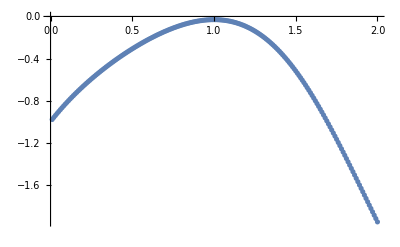

```mathematica
h=0.01;
For[k=1;M=2/h;t=0;x=-1;num={},k≤M,k++,
x1=1+x^2-t^3;
x2=2 x x1-3 t^2;
x3=2 x1^2+2 x x2-6 t;
x4=6 x1 x2+2 x x3-6;
x=x+h(x1+h/2 (x2+h/3 (x3+h/4 x4)));
t=t+h;
AppendTo[num,{t,x}];
];
num
ListPlot[num]
```

{{0.001,-0.998002},{0.002,-0.996008},{0.003,-0.994018},{0.004,-0.992032},1992,{1.997,-1.94476},{1.998,-1.94794},{1.999,-1.95112},{2.,-1.9543}}
 |  |  |  |

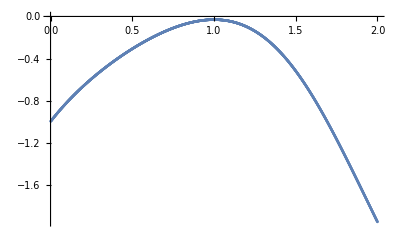

```mathematica
h=0.001;
For[k=1;M=2/h;t=0;x=-1;num={};,k≤M,k++,
x1=1+x^2-t^3;
x2=2 x x1-3 t^2;
x3=2 x1^2+2 x x2-6 t;
x4=6 x1 x2+2 x x3-6;
x=x+h(x1+h/2 (x2+h/3 (x3+h/4 x4)));
t=t+h;
AppendTo[num,{t,x}];
];
num
ListPlot[num]
```